Quick Quantum Computing with Q3

Quantum States in Q3paclet:QuantumMob/Q3/tutorial/QuickQuantumComputingWithQ3#2114153471 | Measurements in Q3paclet:QuantumMob/Q3/tutorial/QuickQuantumComputingWithQ3#616516018
Operators on Qubits in Q3paclet:QuantumMob/Q3/tutorial/QuickQuantumComputingWithQ3#1564669078 | Quantum Circuit Modelpaclet:QuantumMob/Q3/tutorial/QuickQuantumComputingWithQ3#2021838213

Q3 provides many utilities and mechanism to facilitate the study of quantum computation and information. In this document, we explain some basic usages of Q3 in the context of quantum computation and quantum information are explained.

For more advanced applications of Q3, see the Quantum Workbook (2022).

Qubitpaclet:QuantumMob/Q3/ref/QubitQuantumMob Package Symbol | A speciespaclet:QuantumMob/Q3/ref/speciesQuantumMob Package Symbol representing a quantum bit or qubit for short.
Ketpaclet:QuantumMob/Q3/ref/KetQuantumMob Package Symbol | Represents a quantum state of a system of speciespaclet:QuantumMob/Q3/ref/speciesQuantumMob Package Symbol.
Basispaclet:QuantumMob/Q3/ref/BasisQuantumMob Package Symbol | Generates the basis of the Hilbert space associated with a system of speciespaclet:QuantumMob/Q3/ref/speciesQuantumMob Package Symbol.
Matrixpaclet:QuantumMob/Q3/ref/MatrixQuantumMob Package Symbol | Gives the matrix representation of operators on the Hilbert space associated with a system of speciespaclet:QuantumMob/Q3/ref/speciesQuantumMob Package Symbol.
ExpressionForpaclet:QuantumMob/Q3/ref/ExpressionForQuantumMob Package Symbol | Recovers an operator expression from a matrix representation.
Elaboratepaclet:QuantumMob/Q3/ref/ElaborateQuantumMob Package Symbol | Transforms an expression to a more explicit form.
Measurementpaclet:QuantumPlaybook/ref/MeasurementQuantumPlaybook Package Symbol | Represents a measurement of Pauli operators (including tensor products of single-qubit Pauli operators)
MeasurementOddspaclet:QuantumPlaybook/ref/MeasurementOddsQuantumPlaybook Package Symbol | Analyses the probabilities and post-measurement states of a Pauli measurement on a quantum state.

Q3 functions useful in quantum computation and quantum information.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum States in Q3

A quantum bit, or qubit for short, is a quantum two-level system. It is the elementary unit of quantum computers. Each qubit is associated with a two-dimensional Hilbert space (≃ ℂ^2). The computational basis of the Hilbert space is denoted by {0,1}.

The Hilbert space associated with a system of n qubits is constructed with the tensor product of the Hilbert spaces of individual qubits and is isomorphic to ℂ^2⊗ℂ^2⊗⋯⊗ℂ^2=(ℂ^2)^(⊗n). The standard tensor-product basis of the Hilbert space is given by

{s_1⊗s_2⊗⋯⊗s_n:s_k=0,1}.

Any quantum state ψ in the Hilbert space can be expanded in this basis as

ψ=∑_(s_1=0)^1 ∑_(s_2=0)^1 ⋯∑_(s_n=0)^1 s_1⊗s_2⊗⋯⊗s_n c_(s_1 s_2(⋯s)_n)

for some complex coefficients c_(s_1 s_2(⋯s)_n).

Q3 provides two different ways to represent the computational basis states of an n-qubit system.

Using Ketpaclet:ref/Ket[s_1,s_2,…,s_n] to represent tensor-product state s_1⊗s_2⊗⋯⊗s_n. Although it looks simple, this method becomes quickly tedious as the number of qubits increases. This method is suitable for a small system of qubits.

Using Ketpaclet:ref/Ket[<|Spaclet:QuantumMob/Q3/ref/SQuantumMob Package Symbol[1]→s_1,S[2]→s_2,…,S[n]→s_n|>] represent tensor-product state s_1⊗s_2⊗⋯⊗s_n. It may look complicated at the first glance but is more efficient for a larger system of qubits.

### Method Using Ket[…]

In this method, a computational basis state is represented by Ketpaclet:ref/Ket[s_1,s_2,…].

For example, consider a three-qubit system. Here is the standard tensor-product basis of the system.

```mathematica
bs=Basis[3]
```

{0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,1,0,1,1,1,0,1,1,1}

Each state in the above basis is displayed in the bra-ket notation. Internally, Ketpaclet:ref/Ket[…] is used.

```mathematica
InputForm[bs]
```

{Ket[{0, 0, 0}], Ket[{0, 0, 1}], Ket[{0, 1, 0}], Ket[{0, 1, 1}], Ket[{1, 0, 0}], 
 Ket[{1, 0, 1}], Ket[{1, 1, 0}], Ket[{1, 1, 1}]}

A state vector is a linear superposition of the standard basis states.

```mathematica
ket=Ket[{0,1,0}]-I*Ket[{1,0,0}]
```

0,1,0-ⅈ 1,0,0

A state vector can be represented by a column vector in the standard tensor-product basis.

```mathematica
vec=Matrix[ket];
vec//MatrixForm
```

(0
0
1
0
-ⅈ
0
0
0)

The original expression in terms of Ketpaclet:ref/Ket[…] may be recovered with ExpressionFor.

```mathematica
new=ExpressionFor[vec]
```

0,1,0-ⅈ 1,0,0

```mathematica
new-ket
```

0

### Method Using Ketpaclet:ref/Ket[<|⋯|>]

In this method, you need to first choose a symbol, say, S, to denote a group of qubits.

```mathematica
Let[Qubit,S]
```

Symbol S declared as qubit can take flavor indices in the form S[j_1,j_2,…,μ]. The preceding flavor indices j_1,j_2,… specifies a particular qubit in the class denoted by the symbol S. The last flavor index μ=0,1,2,3,… refers to the Pauli operator (I,X,Y,Z,…, respectively, to be discussed below) on the qubit specified by the preceding indices j_1,j_2,…. An exceptional case is μ=$paclet:QuantumMob/Q3/ref/$QuantumMob Package Symbol, and S[j_1,j_2,…,$paclet:QuantumMob/Q3/ref/$QuantumMob Package Symbol] refers to the qubit itself (rather than an operator) specified by the indices j_1,j_2,….

Now, a computational basis state is specified by

Ketpaclet:ref/Ket[<|Spaclet:QuantumMob/Q3/ref/SQuantumMob Package Symbol[1,$]→s_1,S[2,$]→s_2,…,S[n,$]→s_n|>].

For example, the logical basis for qubit S[1,$] is comprised of these two states.

```mathematica
v0=Ket[S[1,$]->0]
v1=Ket[S[1,$]->1]
```

0_(,,S_(,,1))

1_(,,S_(,,1))

They are displayed in the bra-ket notation. Internally, Ketpaclet:ref/Ket[<|⋯|>] is used.

```mathematica
{v0,v1}//InputForm
```

{Ket[<|S[1, $] -> 0|>], Ket[<|S[1, $] -> 1|>]}

For a two-qubit system, here is the standard tensor-product basis. Recall that different qubits (within the same class referred to by symbol S) are distinguished by the flavor indices.

```mathematica
bs=Basis[S[1],S[2]]
bs//InputForm
```

{0_(,,S_(,,1))0_(,,S_(,,2)),0_(,,S_(,,1))1_(,,S_(,,2)),1_(,,S_(,,1))0_(,,S_(,,2)),1_(,,S_(,,1))1_(,,S_(,,2))}

{Ket[<|S[1, $] -> 0, S[2, $] -> 0|>], Ket[<|S[1, $] -> 0, S[2, $] -> 1|>], 
 Ket[<|S[1, $] -> 1, S[2, $] -> 0|>], Ket[<|S[1, $] -> 1, S[2, $] -> 1|>]}

Typing in the special flavor index $ every time you specify a state vector would be cumbersome, and within Ketpaclet:ref/Ket[…], it can be dropped. (Many other functions in Q3 also allow it.)

```mathematica
v0=Ket[S[1]->0]
v1=Ket[S[1]->1]
```

0_(,,S_(,,1))

1_(,,S_(,,1))

Note that any unspecified qubit is supposed to be initialized in state Ketpaclet:ref/Ket[0].

```mathematica
ket=v0-I v1
KetRegulate[ket,{S[1,$],S[2,$]}]
KetRegulate[ket,{S[1],S[2]}]
```

0_(,,S_(,,1))-ⅈ 1_(,,S_(,,1))

0_(,,S_(,,1))0_(,,S_(,,2))-ⅈ 1_(,,S_(,,1))0_(,,S_(,,2))

0_(,,S_(,,1))0_(,,S_(,,2))-ⅈ 1_(,,S_(,,1))0_(,,S_(,,2))

A state vector can be represented by a column vector in the standard tensor-product basis (computational basis). This can be achieved by Matrixpaclet:QuantumMob/Q3/ref/MatrixQuantumMob Package Symbol. For example, consider the following state.

```mathematica
ket=S[1,6]**S[2,6]**Ket[]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))+1/2 0_(,,S_(,,1))1_(,,S_(,,2))+1/2 1_(,,S_(,,1))0_(,,S_(,,2))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))

Get the column-vector representation of it.  Here note that S[{1,2}]={S[1],S[2]} is equivalent to S[{1,2},$paclet:ref/$]={S[1,$paclet:ref/$],S[2,$paclet:ref/$]} inside Matrixpaclet:QuantumMob/Q3/ref/MatrixQuantumMob Package Symbol.

```mathematica
vec=Matrix[ket,S@{1,2}];
vec//MatrixForm
```

(1/2
1/2
1/2
1/2)

Recover the expression in terms of basis states. (Again, $ is automatically attached unless it already exists inside ExpressionForpaclet:QuantumMob/Q3/ref/ExpressionForQuantumMob Package Symbol.)

```mathematica
new=ExpressionFor[vec,S@{1,2}]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))+1/2 0_(,,S_(,,1))1_(,,S_(,,2))+1/2 1_(,,S_(,,1))0_(,,S_(,,2))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))

Operators on Qubits in Q3

Any linear operator U on the Hilbert space associated with a system of n qubits can be written as a linear combination of tensor products of single-qubit Pauli operators,

U=∑_(μ_1=0)^4 ∑_(μ_2=0)^4 ⋯∑_(μ_n=0)^4 S^μ_1⊗S^μ_2⊗…⊗S^μ_n c_(μ_1 μ_2... μ_n),

where μ_k=0,1,2,3 with S^0=I, S^1=X, S^2=Y, S^3=Z, and c_(μ_1 μ_2... μ_n) are complex coefficients.

Like state vectors, Q3 provides two different ways to represent the Pauli operators.

Using Paulipaclet:QuantumMob/Q3/ref/PauliQuantumMob Package Symbol[μ_1,μ_2,…,μ_n] to represent tensor product S^μ_1⊗S^μ_2⊗…⊗S^μ_n. This method works consistently with the method using Ketpaclet:ref/Ket[s_1,s_2,…,s_n] for tensor-product basis states. This method is suitable for a small system of qubits.

Using S[j_1,μ_1]**S[j_2,μ_2]**⋯**S[j_n,μ_n](here **  is NonCommutativeMultiplypaclet:ref/NonCommutativeMultiply or Multiplypaclet:QuantumMob/Q3/ref/MultiplyQuantumMob Package Symbol for short) to represent tensor product S^μ_1⊗S^μ_2⊗…⊗S^μ_n. This method works consistently with the method using Ketpaclet:ref/Ket[<|…|>] to represent tensor-product basis state. This method may look complicated at the first glance but is more efficient for a larger system of qubits.

### Method Using Paulipaclet:QuantumMob/Q3/ref/PauliQuantumMob Package Symbol[⋯]

Consider a tensor product of single-qubit Pauli operators.

```mathematica
op=Pauli[{1,0,2}]
```

X⊗I⊗Y

Consider a state vector.

```mathematica
in=Ket[{0,1,0}]-Ket[{1,0,0}]
```

0,1,0-1,0,0

You can act operator op on the above state vector using Multiply or, equivalently, **.

```mathematica
out=op**in
```

-ⅈ 0,0,1+ⅈ 1,1,1

The matrix representation of an operator in the standard tensor-product basis can be obtained using Matrixpaclet:QuantumMob/Q3/ref/MatrixQuantumMob Package Symbol.

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0)

The operator expression may be recovered with ExpressionFor.

```mathematica
new=ExpressionFor[mat]//Elaborate
```

X⊗I⊗Y

```mathematica
op-new
```

0

### Method Using S[⋯]**S[⋯]**⋯

This is a typical form of a linear operator in this method. Recall that S[j_1,j_2,…,μ] operates on qubit S[j_1,j_2,…,$paclet:ref/$].

```mathematica
op=S[1,1]+I S[1,2]**S[2,2]
```

ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Y)+S_(,,1)^(,,X)

```mathematica
op//PauliForm
```

X⊗I+ⅈ Y⊗Y

Consider a state vector.

```mathematica
in=Ket[S@{1,2}]
```

0_(,,S_(,,1))0_(,,S_(,,2))

You can act operator op on the above state vector using Multiply (**).

```mathematica
out=op**in
```

1_(,,S_(,,1))0_(,,S_(,,2))-ⅈ 1_(,,S_(,,1))1_(,,S_(,,2))

Matrixpaclet:QuantumMob/Q3/ref/MatrixQuantumMob Package Symbol converts the operator into a matrix representation in the standard basis of the qubits involved in the expression.

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 1 | -ⅈ
0 | 0 | ⅈ | 1
1 | ⅈ | 0 | 0
-ⅈ | 1 | 0 | 0)

It is a good habit to check the standard basis implied in the matrix representation.

```mathematica
bs=Basis[S[1],S[2]]
```

{0_(,,S_(,,1))0_(,,S_(,,2)),0_(,,S_(,,1))1_(,,S_(,,2)),1_(,,S_(,,1))0_(,,S_(,,2)),1_(,,S_(,,1))1_(,,S_(,,2))}

You can recover the operator expression from the matrix representation using ExpressionForpaclet:QuantumMob/Q3/ref/ExpressionForQuantumMob Package Symbol.

```mathematica
new=ExpressionFor[mat,S@{1,2}]//Elaborate
op-new
```

ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Y)+S_(,,1)^(,,X)

0

MultiplyExppaclet:QuantumMob/Q3/ref/MultiplyExpQuantumMob Package Symbol is another way to generate an operator from other operator.

```mathematica
expr=MultiplyExp[-I S[1,2] ϕ]
Elaborate[expr]
```

ⅇ^(-ⅈ ϕ S_(,,1)^(,,Y))

Cos[ϕ]-ⅈ S_(,,1)^(,,Y) Sin[ϕ]

Sometimes, it is useful to collectively refer to different Pauli operators on the same qubit. S[j_1,j_2,…,Allpaclet:ref/All] and S[j_1,j_2,…,Fullpaclet:ref/Full] are reserved for this purpose.

```mathematica
S[1,All]
S[2,Full]
```

{S_(,,1)^(,,X),S_(,,1)^(,,Y),S_(,,1)^(,,Z)}

{S_(,,2)^(,,0),S_(,,2)^(,,X),S_(,,2)^(,,Y),S_(,,2)^(,,Z)}

Use the above sets to construct some composite expressions. For example, you can construct 
the Heisenberg Hamiltonian for two spins (qubits).

```mathematica
op=Total[S[1,All]**S[2,All]]
PauliForm[op]
```

S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,1)^(,,Y)S_(,,2)^(,,Y)+S_(,,1)^(,,Z)S_(,,2)^(,,Z)

X⊗X+Y⊗Y+Z⊗Z

Measurements in Q3

Q3 supports measurement of any Pauli operators (including tensor products of single-qubit Pauli operators).

As a simple example, consider a three-qubit system in the following state.

```mathematica
in=(Ket[S@{1,2,3}->0]+Ket[S@{1,2,3}->1])/Sqrt[2]
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))+1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(√2)

Suppose that you want to measure the Pauli Z operator (i.e., S[1,3]) on qubit S[1,$]. From the above state, we expect two measurement outcomes 0 and 1 (corresponding to eigenvalues ±1 of S[1,3]) and corresponding post-measurement states with equal probability.

```mathematica
MeasurementOdds[S[1,3]][in]
```

<|0→{1/2,0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))},1→{1/2,1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))}|>

Performing the measurement, you can get random outcomes according to the probabilities shown above.

```mathematica
out=Measurement[S[1,3]][in]
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))

```mathematica
msr=Measurement[S[1,3]];
Table[msr[in],10]
```

{1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))}

```mathematica
Table[msr[in];Readout[S[1,3]],10]
```

{0,1,1,1,0,1,1,0,0,1}

Collecting the random outcomes, you can infer the probability distribution.

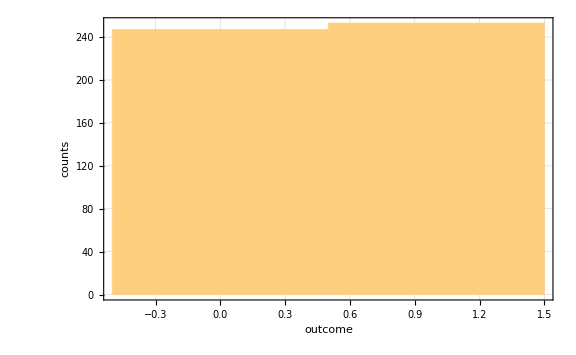

```mathematica
data=Table[msr[in];Readout[S[1,3]],500];
Histogram[data,FrameLabel->{"outcome","counts"}]
```

As another example, let us now consider a collective measurement, say, the measurement of Z⊗Z. Suppose that a system of two qubits in the following state.

```mathematica
in=Basis[S@{1,2}].{1,1,I,-I}
```

0_(,,S_(,,1))0_(,,S_(,,2))+0_(,,S_(,,1))1_(,,S_(,,2))+ⅈ 1_(,,S_(,,1))0_(,,S_(,,2))-ⅈ 1_(,,S_(,,1))1_(,,S_(,,2))

Analyse the possible measurement outcomes, the corresponding probabilities and post-measurement states. Here note that outcomes 0 and 1 refer to eigenvalues ±1 of Z⊗Z, respectively. (Recall that any Pauli operator only has eigenvalues ±1.) It is also important to note that the post-measurement states maintains the phase coherence inherited from the input state.

```mathematica
MeasurementOdds[S[1,3]**S[2,3]][in]
```

<|0→{1/2,(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)-(ⅈ 1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)},1→{1/2,(0_(,,S_(,,1))1_(,,S_(,,2)))/(√2)+(ⅈ 1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)}|>

As in the above example, one can infer the probability distribution by sampling the outcomes.

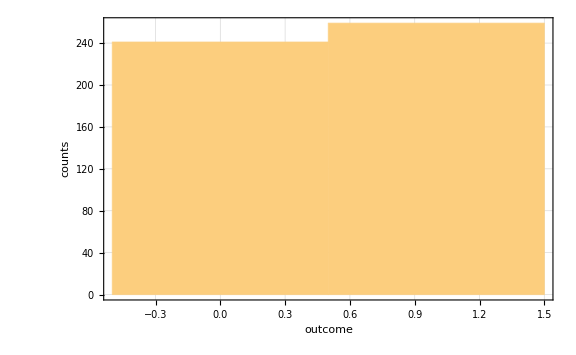

```mathematica
data=Table[Measurement[S[1,3]**S[2,3]][in];Readout[S[1,3]**S[2,3]],500];
Histogram[data,FrameLabel->{"outcome","counts"}]
```

Quantum Circuit Model

Q3 fully supports the quantum circuit model of quantum computation through QuantumCircuitpaclet:QuantumMob/Q3/ref/QuantumCircuitQuantumMob Package Symbol.

S[j_1,j_2,…,1|2|3] | The Pauli X, Y, and Z, respectively, on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,6] | The Hadamard gate on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,7] | The quadrant phase gate on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,8] | The octant phase gate on qubit S[j_1,j_2,…,$].
Rotationpaclet:QuantumMob/Q3/ref/RotationQuantumMob Package Symbol | Single-qubit rotation gate.
Phasepaclet:QuantumMob/Q3/ref/PhaseQuantumMob Package Symbol | Single-qubit (relative) phase shift.
CNOTpaclet:QuantumMob/Q3/ref/CNOTQuantumMob Package Symbol | The CNOT gate.
Toffolipaclet:QuantumMob/Q3/ref/ToffoliQuantumMob Package Symbol | The Toffoli gate.
Fredkinpaclet:QuantumMob/Q3/ref/FredkinQuantumMob Package Symbol | The Fredkin gate.
ControlledGatepaclet:QuantumMob/Q3/ref/ControlledGateQuantumMob Package Symbol | Controlled-unitary gate.
Oraclepaclet:QuantumMob/Q3/ref/OracleQuantumMob Package Symbol | Quantum oracle.

Some frequently used quantum circuit elements in the quantum circuit model of quantum computation.

Here is an simple example of quantum circuit.

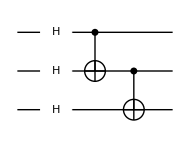

```mathematica
qc=QuantumCircuit[S[{1,2,3},6],CNOT[S[1],S[2]],CNOT[S[2],S[3]]]
```

One can convert a quantum circuit to an analytic expression.

```mathematica
op=ExpressionFor[qc]
```

-1/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X))/(4 √2)-(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Y))/(4 √2)+(S_(,,1)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Z))/(4 √2)-(S_(,,1)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,X)S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Y)S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)-(S_(,,1)^(,,Y)S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,1)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z))/(4 √2)+(ⅈ S_(,,3)^(,,Y))/(4 √2)

One can also directly apply a quantum circuit to an input state.

```mathematica
in=Ket[S@{1,2,3}]
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))

```mathematica
out=qc**in
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)

The above output state should be the same as the result from acting operator expression op.

```mathematica
new=op**in
```

(0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(2 √2)+(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(2 √2)

```mathematica
out-new
```

0

It is possible to multiply the quantum circuit with an operator as well.

```mathematica
qc**S[1,1]
op**S[1,1]
```

(S_(,,1)^(,,X)S_(,,2)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,3)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X))/(4 √2)+(S_(,,1)^(,,Y)S_(,,2)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Y)S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,X))/(4 √2)-(S_(,,1)^(,,Z))/(4 √2)+(S_(,,2)^(,,X))/(4 √2)-(ⅈ S_(,,2)^(,,Y))/(4 √2)+(S_(,,3)^(,,X))/(4 √2)+(S_(,,3)^(,,Z))/(4 √2)

(S_(,,1)^(,,X)S_(,,2)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,3)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X))/(4 √2)+(S_(,,1)^(,,Y)S_(,,2)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Y)S_(,,2)^(,,X)S_(,,3)^(,,Y))/(4 √2)-(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Y)S_(,,3)^(,,Y))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X))/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Z))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,X))/(4 √2)-(S_(,,1)^(,,Z))/(4 √2)+(S_(,,2)^(,,X))/(4 √2)-(ⅈ S_(,,2)^(,,Y))/(4 √2)+(S_(,,3)^(,,X))/(4 √2)+(S_(,,3)^(,,Z))/(4 √2)

| Related Guides
▪Quantum Information Systems
▪Q3: Symbolic Quantum Simulation

| Related Tech Notes
▪The Postulates of Quantum Mechanics
▪Quantum Computation: Overview
▪Quantum Algorithms
▪Quantum Noise and Decoherence
▪Quantum Error-Correction Codes
▪Quantum Information Theory

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttp://www.wolfram.com/language/fast-introduction-for-programmers/